```mathematica
f[x_]=2x^2-x^3;
a=0;
b=2;
```

```mathematica
RevolutionPlot3D[f[x],{x,a,b}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{f[x]Cos[r],f[x]Sin[r],x},{x,a,b},{r,0,2 Pi}]
```

-Graphics3D-

WolframAlphaQueryParseResults

```mathematica
ParametricPlot3D[{x,(2-f[x])Cos[r],(2-f[x])Sin[r]},{x,a,b},{r,0,2 Pi}]
```

-Graphics3D-

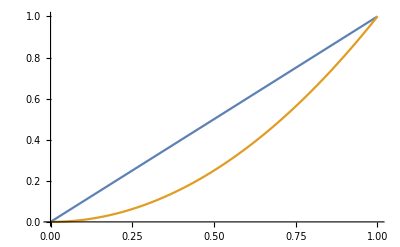

```mathematica
Plot[{x,x^2},{x,0,1}]
```

```mathematica
RevolutionPlot3D[{x,x^2},{x,0,1}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{{x,x Cos[t],x Sin[t]},{x,x^2 Cos[t],x^2 Sin[t]}},{x,0,1},{t,0,2 Pi}]
```

-Graphics3D-